```mathematica
f1[x_,theta_]:=1/theta*Exp[-x/theta];
f[x_,theta_,c_,eps_]:=(1-eps)*f1[x,theta]+eps*f1[x,c];
Lq[u_,q_]:=(u^(1-q)-1)/(1-q);
(*phi[x_,theta_,q_]:=D[Lq[f1[x,theta],q],theta];*)
phi[x_,theta_,q_]:=((ⅇ^(-x/theta)/theta)^(1-q) (-theta+x))/theta^2;
(*phip[x_,theta_,q_]:=D[Lq[f1[x,theta],q],theta,theta];*)
phip[x_,theta_,q_]:=((ⅇ^(-x/theta)/theta)^(1-q) (-(-2+q) theta^2+2 (-2+q) theta x-(-1+q) x^2))/theta^4;
```

```mathematica
Integrate[(phi[x,thetaP,q])*f[x,theta0,c,eps],{x,0,Infinity},Assumptions->{thetaP∈Reals,thetaP>0,theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q≥0,q≤1,c∈Reals,c>0}]
```

thetaP^(-1+q) ((c eps)/(c-c q+thetaP)^2-eps/(c-c q+thetaP)-((-1+eps) theta0)/(theta0-q theta0+thetaP)^2+(-1+eps)/(theta0-q theta0+thetaP))

```mathematica
Collect[c eps(theta0-q theta0+thetaP)^2-eps(c-c q+thetaP)(theta0-q theta0+thetaP)^2-(-1+eps) theta0(c-c q+thetaP)^2+(-1+eps)(theta0-q theta0+thetaP)(c-c q+thetaP)^2,thetaP]
```

c^2 (1-eps) theta0+c^2 (-1+eps) theta0-2 c^2 (1-eps) q theta0-3 c^2 (-1+eps) q theta0+c^2 (1-eps) q^2 theta0+3 c^2 (-1+eps) q^2 theta0-c^2 (-1+eps) q^3 theta0+c eps q theta0^2-2 c eps q^2 theta0^2+c eps q^3 theta0^2+(c^2 (-1+eps)-2 c^2 (-1+eps) q+c^2 (-1+eps) q^2+2 c (1-eps) theta0+2 c (-1+eps) theta0-2 c (1-eps) q theta0-4 c (-1+eps) q theta0+2 c eps q theta0+2 c (-1+eps) q^2 theta0-2 c eps q^2 theta0-eps theta0^2+2 eps q theta0^2-eps q^2 theta0^2) thetaP+(2 c (-1+eps)-2 c (-1+eps) q+c eps q+(1-eps) theta0+(-1+eps) theta0-2 eps theta0+(1-eps) q theta0+2 eps q theta0) thetaP^2-thetaP^3

```mathematica
FullSimplify[CubeRoot[qTmp[theta0,q,c,eps]+(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+CubeRoot[qTmp[theta0,q,c,eps]-(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+pTmp[theta0,q,c,eps],Assumptions->{theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤0.5,q∈Reals,q>0,q≤1,c∈Reals,c>0}]
```

1/3 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-3 c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0)+(-1+q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))-√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-3 c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0)+(-1+q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-3 c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0)+(-1+q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-3 c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0)+(-1+q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3)

```mathematica
FullSimplify[qTmp[theta0,q,c,eps]+(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2),Assumptions->{theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤0.5,q∈Reals,q>0,q≤1,c∈Reals,c>0}]
```

1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2+1/3 (-1+q) (c^2 (-1+eps+q-eps q)+2 c q theta0+eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2)

```mathematica
FullSimplify[CubeRoot[qTmp[theta0,q,c,eps]+(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+CubeRoot[qTmp[theta0,q,c,eps]-(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+pTmp[theta0,q,c,eps]]
```

```mathematica
aTmp[theta0_,q_,c_,eps_]:=-1;
bTmp[theta0_,q_,c_,eps_]:=c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0;
cTmp[theta0_,q_,c_,eps_]:=(-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2);
dTmp[theta0_,q_,c_,eps_]:=-c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0);
pTmp[theta0_,q_,c_,eps_]:=-bTmp[theta0,q,c,eps]/3/aTmp[theta0,q,c,eps];
(*qTmp[theta0_,q_,c_,eps_]:=(pTmp[theta0,q,c,eps])^3+(bTmp[theta0,q,c,eps]*cTmp[theta0,q,c,eps]-3aTmp[theta0,q,c,eps]*dTmp[theta0,q,c,eps])/(6*(aTmp[theta0,q,c,eps])^2);*)
qTmp[theta0_,q_,c_,eps_]:=1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2));
rTmp[theta0_,q_,c_,eps_]:=cTmp[theta0,q,c,eps]/3/aTmp[theta0,q,c,eps];
thetaP[theta0_,q_,c_,eps_]:=CubeRoot[qTmp[theta0,q,c,eps]+(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+CubeRoot[qTmp[theta0,q,c,eps]-(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+pTmp[theta0,q,c,eps];
```

```mathematica
thetaP[theta,q,c,eps]
```

1/3 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^3+1/6 (-1+q) (-3 c (-1+q) q theta (c (-1+eps)-eps theta)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2))-√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^3+1/6 (-1+q) (-3 c (-1+q) q theta (c (-1+eps)-eps theta)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2)))^2))^(1/3)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^3+1/6 (-1+q) (-3 c (-1+q) q theta (c (-1+eps)-eps theta)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta)^3+1/6 (-1+q) (-3 c (-1+q) q theta (c (-1+eps)-eps theta)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta) (c^2 (-1+eps) (-1+q)-2 c q theta-eps (-1+q) theta^2)))^2))^(1/3)

```mathematica
FullSimplify[thetaP[theta,1,c,eps]]
```

c eps+theta-eps theta

```mathematica
Integrate[(phi[x,thetaP0,q])^2*f[x,theta0,c,eps],{x,0,Infinity},Assumptions->{thetaP0∈Reals,thetaP0>0,theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q>0,q≤1,c∈Reals,c>0}]
```

thetaP0^(-3+2 q) ((2 c^2 eps)/(-2 c (-1+q)+thetaP0)^3-(2 c eps)/(-2 c (-1+q)+thetaP0)^2+eps/(2 c-2 c q+thetaP0)-(2 (-1+eps) theta0^2)/(-2 (-1+q) theta0+thetaP0)^3+(2 (-1+eps) theta0)/(-2 (-1+q) theta0+thetaP0)^2+(1-eps)/(2 theta0-2 q theta0+thetaP0))

```mathematica
Ephi2[theta0_,q_,eps_,c_,thetaP0_]:=thetaP0^(-3+2 q) ((2 c^2 eps)/(-2 c (-1+q)+thetaP0)^3-(2 c eps)/(-2 c (-1+q)+thetaP0)^2+eps/(2 c-2 c q+thetaP0)-(2 (-1+eps) theta0^2)/(-2 (-1+q) theta0+thetaP0)^3+(2 (-1+eps) theta0)/(-2 (-1+q) theta0+thetaP0)^2+(1-eps)/(2 theta0-2 q theta0+thetaP0));
```

```mathematica
Simplify[Ephi2[theta0,1,eps,c,thetaP0]]
```

(2 c^2 eps-2 (-1+eps) theta0^2-2 c eps thetaP0+2 (-1+eps) theta0 thetaP0+thetaP0^2)/thetaP0^4

```mathematica
Integrate[phip[x,thetaP0,q]*f[x,theta0,c,eps],{x,0,Infinity},Assumptions->{thetaP0∈Reals,thetaP0>0,theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q>0,q≤1,c∈Reals,c>0}]
```

thetaP0^(-2+q) ((2 c^2 eps (-1+q))/(c (-1+q)-thetaP0)^3+(2 c eps (-2+q))/(c-c q+thetaP0)^2+(q^3 theta0^2-2 thetaP0^2-2 q^2 theta0 (theta0+thetaP0)+q (theta0^2+4 theta0 thetaP0+thetaP0^2))/((-1+q) theta0-thetaP0)^3+eps (2/(c-c q+thetaP0)-(2 theta0^2)/(theta0-q theta0+thetaP0)^3+(4 theta0)/(theta0-q theta0+thetaP0)^2-2/(theta0-q theta0+thetaP0)+q (-1/(c-c q+thetaP0)+(2 theta0^2)/(theta0-q theta0+thetaP0)^3-(2 theta0)/(theta0-q theta0+thetaP0)^2+1/(theta0-q theta0+thetaP0))))

```mathematica
FullSimplify[%20]
```

thetaP0^(-2+q) (-(2 c^2 eps (-1+q))/(c-c q+thetaP0)^3+(2 c eps (-2+q))/(c-c q+thetaP0)^2-(eps (-2+q))/(c-c q+thetaP0)+(2 (-1+eps) (-1+q) theta0^2)/(theta0-q theta0+thetaP0)^3-(2 (-1+eps) (-2+q) theta0)/(theta0-q theta0+thetaP0)^2+((-1+eps) (-2+q))/(theta0-q theta0+thetaP0))

```mathematica
Ephip[theta0_,q_,eps_,c_,thetaP0_]:=thetaP0^(-2+q) (-(2 c^2 eps (-1+q))/(c-c q+thetaP0)^3+(2 c eps (-2+q))/(c-c q+thetaP0)^2-(eps (-2+q))/(c-c q+thetaP0)+(2 (-1+eps) (-1+q) theta0^2)/(theta0-q theta0+thetaP0)^3-(2 (-1+eps) (-2+q) theta0)/(theta0-q theta0+thetaP0)^2+((-1+eps) (-2+q))/(theta0-q theta0+thetaP0));
```

```mathematica
Simplify[Ephip[theta0,1,eps,c,thetaP0]]
```

(-2 c eps+2 (-1+eps) theta0+thetaP0)/thetaP0^3

```mathematica
FullSimplify[(Ephi2[theta0,1,eps,c,c eps+theta0-eps theta0]/(Ephip[theta0,1,eps,c,c eps+theta0-eps theta0])^2)]
```

-c^2 (-2+eps) eps+2 c (-1+eps) eps theta0-(-1+eps^2) theta0^2

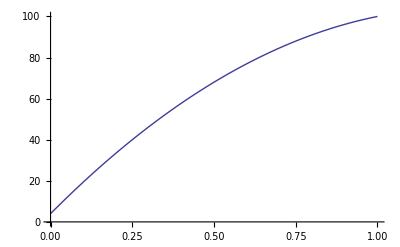

```mathematica
Plot[-c^2 (-2+eps) eps+2 c (-1+eps) eps theta0-(-1+eps^2) theta0^2/.{theta0->2,c->10},{eps,0,1}]
```

```mathematica
FullSimplify[(Ephi2[theta0,q,eps,c,thetaP0]/(Ephip[theta0,q,eps,c,thetaP0])^2)/(Ephi2[theta0,1,eps,c,thetaP0]/(Ephip[theta0,1,eps,c,thetaP0])^2)]
```

```mathematica
FullSimplify[(thetaP0^(-3+2,q),((2,c^2,eps)/(-2,c,(-1+q)+thetaP0)^3-(2,c,eps)/(-2,c,(-1+q)+thetaP0)^2+eps/(2,c-2,c,q+thetaP0)-(2,(-1+eps),theta0^2)/(-2,(-1+q),theta0+thetaP0)^3+(2,(-1+eps),theta0)/(-2,(-1+q),theta0+thetaP0)^2+(1-eps)/(2,theta0-2,q,theta0+thetaP0)))/(thetaP0^(-2+q),(-(2,c^2,eps,(-1+q))/(c-c,q+thetaP0)^3+(2,c,eps,(-2+q))/(c-c,q+thetaP0)^2-(eps,(-2+q))/(c-c,q+thetaP0)+(2,(-1+eps),(-1+q),theta0^2)/(theta0-q,theta0+thetaP0)^3-(2,(-1+eps),(-2+q),theta0)/(theta0-q,theta0+thetaP0)^2+((-1+eps),(-2+q))/(theta0-q,theta0+thetaP0))),Assumptions->{thetaP0∈Reals,thetaP0>0,theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q>0,q≤1,c∈Reals,c>0}]
```

```mathematica
(thetaP0^(-1+q),((2,c^2,eps)/(-2,c,(-1+q)+thetaP0)^3-(2,c,eps)/(-2,c,(-1+q)+thetaP0)^2+eps/(2,c-2,c,q+thetaP0)-(2,(-1+eps),theta0^2)/(-2,(-1+q),theta0+thetaP0)^3+(2,(-1+eps),theta0)/(-2,(-1+q),theta0+thetaP0)^2+(1-eps)/(2,theta0-2,q,theta0+thetaP0)))/(-(2,c^2,eps,(-1+q))/(c-c,q+thetaP0)^3+(2,c,eps,(-2+q))/(c-c,q+thetaP0)^2-(eps,(-2+q))/(c-c,q+thetaP0)+(2,(-1+eps),(-1+q),theta0^2)/(theta0-q,theta0+thetaP0)^3-(2,(-1+eps),(-2+q),theta0)/(theta0-q,theta0+thetaP0)^2+((-1+eps),(-2+q))/(theta0-q,theta0+thetaP0))
```

```mathematica
a={0.8605,0.8637,1.1044,2.5588,1.7027,0.3643,1.8286,1.6245,2.9520,8.4457,0.2450,0.1894,0.2456,0.1907,1.8400,1.1327,3.0820,1.2717,2.8141,2.3780};
```

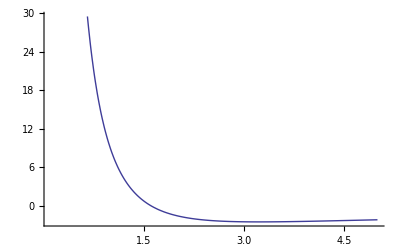

```mathematica
Plot[Sum[(1/theta*Exp[-a[[i]]/theta])^(1-q)*(a[[i]]-theta)/theta^2,{i,20}]/.{q->0.9},{theta,0.1,5}]
```

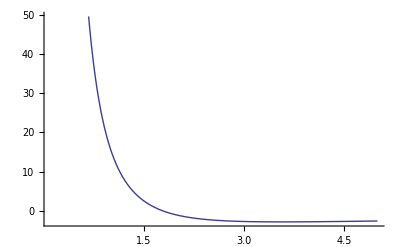

```mathematica
Plot[Sum[(a[[i]]-theta)/theta^2,{i,20}]/.{q->0.9},{theta,0.1,5}]
```

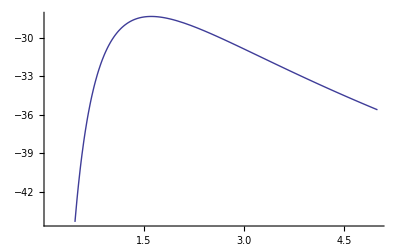

```mathematica
Plot[Sum[((1/theta*Exp[-a[[i]]/theta])^(1-q)-1)/(1-q),{i,20}]/.{q->0.9},{theta,0.1,5}]
```

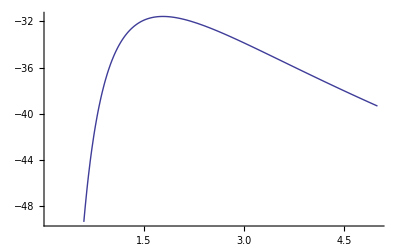

```mathematica
Plot[Sum[(-Log[theta]-a[[i]]/theta),{i,20}]/.{q->0.9},{theta,0.1,5}]
```

```mathematica
a
```

{0.8605,0.8637,1.1044,2.5588,1.7027,0.3643,1.8286,1.6245,2.952,8.4457,0.245,0.1894,0.2456,0.1907,1.84,1.1327,3.082,1.2717,2.8141,2.378}

```mathematica
Mean[a]
```

1.78472